```mathematica
model="phi";
loadNotebook["inz_off_model_"<>model<>".nb"];
q̇ // Simplify // MF
```

(R (Sin[θ_0] η_1+Cos[θ_0] Cos[ϕ_1] η_2+(Sin[θ_0] Sin[θ_1]-Cos[θ_0] Cos[θ_1] Sin[ϕ_1]) η_3)
R (-Cos[θ_0] η_1+Cos[ϕ_1] Sin[θ_0] η_2-(Cos[θ_0] Sin[θ_1]+Cos[θ_1] Sin[θ_0] Sin[ϕ_1]) η_3)
(R (-Cos[ϕ_1] η_2+Cos[θ_1] Sin[ϕ_1] η_3+Cos[ϕ_2] η_4-Cos[θ_2] Sin[ϕ_2] η_5))/(2 l)
η_1
η_2
η_3
η_1+Sin[θ_1] η_3-Sin[θ_2] η_5
η_4
η_5)

```mathematica
G2//Simplify//MF
G3=G2;
G3[[1,1]]=0;
G3[[1,2]]=0;
G3[[2,1]]=0;
G3[[2,2]]=0;
G3[[3,2]]=0;
G3[[3,4]]=0;
G3//Simplify//MF
```

(R Sin[θ_0[t]] | R Cos[θ_0[t]] Cos[ϕ_1[t]] | R (Sin[θ_0[t]] Sin[θ_1[t]]-Cos[θ_0[t]] Cos[θ_1[t]] Sin[ϕ_1[t]]) | 0 | 0
-R Cos[θ_0[t]] | R Cos[ϕ_1[t]] Sin[θ_0[t]] | -R (Cos[θ_0[t]] Sin[θ_1[t]]+Cos[θ_1[t]] Sin[θ_0[t]] Sin[ϕ_1[t]]) | 0 | 0
0 | -(R Cos[ϕ_1[t]])/(2 l) | (R Cos[θ_1[t]] Sin[ϕ_1[t]])/(2 l) | (R Cos[ϕ_2[t]])/(2 l) | -(R Cos[θ_2[t]] Sin[ϕ_2[t]])/(2 l)
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | Sin[θ_1[t]] | 0 | -Sin[θ_2[t]]
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

(0 | 0 | R (Sin[θ_0[t]] Sin[θ_1[t]]-Cos[θ_0[t]] Cos[θ_1[t]] Sin[ϕ_1[t]]) | 0 | 0
0 | 0 | -R (Cos[θ_0[t]] Sin[θ_1[t]]+Cos[θ_1[t]] Sin[θ_0[t]] Sin[ϕ_1[t]]) | 0 | 0
0 | 0 | (R Cos[θ_1[t]] Sin[ϕ_1[t]])/(2 l) | 0 | -(R Cos[θ_2[t]] Sin[ϕ_2[t]])/(2 l)
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | Sin[θ_1[t]] | 0 | -Sin[θ_2[t]]
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
wyliczSterowanie[wd_,w_,k1_,k2_]:=(
G3=G2;
G3[[1,1]]=0;
G3[[1,2]]=0;
G3[[2,1]]=0;
G3[[2,2]]=0;
G3[[3,2]]=0;
G3[[3,4]]=0;
eta={Subscript[η, 1][t],Subscript[η, 2][t],Subscript[η, 3][t],Subscript[η, 4][t],Subscript[η, 5][t]};
uklad=Transpose[G3.Transpose[{{Subscript[η, 1][t],Subscript[η, 2][t],Subscript[η, 3][t],Subscript[η, 4][t],Subscript[η, 5][t]}}]][[1]];
podstawienie = {D[x[t],t]->uklad[[1]],D[y[t],t]->uklad[[2]],D[Subscript[θ, 0][t],t]->uklad[[3]],D[Subscript[ϕ, 1][t],t]->uklad[[4]],D[Subscript[θ, 1][t],t]->uklad[[5]],D[Subscript[ψ, 1][t],t]->uklad[[6]],D[Subscript[ϕ, 2][t],t]->uklad[[7]],D[Subscript[θ, 2][t],t]->uklad[[8]],D[Subscript[ψ, 2][t],t]->uklad[[9]]};
wp=D[w,t] /. podstawienie;
wpp=D[wp,t]/.podstawienie;
dcoe={Coefficient[wpp,D[Subscript[η, 1][t],t]],Coefficient[wpp,D[Subscript[η, 2][t],t]],Coefficient[wpp,D[Subscript[η, 3][t],t]],Coefficient[wpp,D[Subscript[η, 4][t],t]],Coefficient[wpp,D[Subscript[η, 5][t],t]]} // Simplify;
coe={Coefficient[wpp,Subscript[η, 1][t]],Coefficient[wpp,Subscript[η, 2][t]],Coefficient[wpp,Subscript[η, 3][t]],Coefficient[wpp,Subscript[η, 4][t]],Coefficient[wpp,Subscript[η, 5][t]]} // Simplify;
test = dcoe//Simplify;
test={ToString[test[[1]]]=="{0, 0, 0, 0, 0}",ToString[test[[2]]]=="{0, 0, 0, 0, 0}",ToString[test[[3]]]=="{0, 0, 0, 0, 0}",ToString[test[[4]]]=="{0, 0, 0, 0, 0}",ToString[test[[5]]]=="{0, 0, 0, 0, 0}"};
Kdd={If[test[[1]],coe[[1]],dcoe[[1]]],If[test[[2]],coe[[2]],dcoe[[2]]],If[test[[3]],coe[[3]],dcoe[[3]]],If[test[[4]],coe[[4]],dcoe[[4]]],If[test[[5]],coe[[5]],dcoe[[5]]]} // Transpose;
Det[Kdd] // Simplify //Print;
P =wpp-Kdd.Table[If[test[[i]],eta[[i]],D[eta[[i]],t]],{i,{1,2,3,4,5}}] // Simplify;
K1 = k1*IdentityMatrix[5];
K2 = k2*IdentityMatrix[5];
sterowanie=Inverse[Kdd].(-P+D[D[wd,t],t]-K1.(D[w,t]-D[wd,t])-K2.(w-wd)) /. {l-> 0.1};
{test,sterowanie}
);

rozwiazRownania[sterowanie_,test_,q0_,tmax_]:=(
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
sterbez={};
q01={};
For[j=1,j<6,j++,If[test[[j]],AppendTo[sterbez,eta[[j]]->sterowanie[[j]]];,lstrona=Join[lstrona,{D[eta[[j]],t]}];
pstrona=Join[pstrona,{sterowanie[[j]]}];
AppendTo[q01,(eta[[j]]/.{t->0})==10];]];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.sterbez~Join~{l-> 0.1,R->0.03}) ~Join~ q0~Join~q01;
tosolve=tosolve/.{l-> 0.1,R->0.03};
roz = NDSolve[tosolve, {x,y, Subscript[θ, 0],Subscript[ϕ, 1], Subscript[θ, 1],Subscript[ψ, 1], Subscript[ϕ, 2], Subscript[θ, 2],Subscript[ψ, 2],Subscript[η, 3],Subscript[η, 5]}, {t,0,tmax}, Method->{"EquationSimplification"->"Residual"} , MaxSteps->1000000];
roz
);

wyrysuj[rozwiazanie_, tmax_,anim_,i_]:=Module[{},
loc="C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\";
weight="Bold";
size=15;

Plot[{x[t]-xd[t]/.rozwiazanie,y[t]-yd[t]/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->All, PlotStyle->{Thick},BaseStyle->{FontWeight->weight,FontSize->size}]//Print;

plot1=Plot[{x[t]-xd[t]/.rozwiazanie,y[t]-yd[t]/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->zakres, PlotStyle->{Thick},BaseStyle->{FontWeight->weight,FontSize->size}];
plot1//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_1.pdf",plot1];

Plot[{Subscript[θ, 0][t]-θd[t]/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_θ_0","e_ψ_1","e_ψ_2"},{0.90,0.75}],PlotRange->All, PlotStyle->{Thick},BaseStyle->{FontWeight->weight,FontSize->size}]//Print;

plot2=Plot[{Subscript[θ, 0][t]-θd[t]/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_θ_0","e_ψ_1","e_ψ_2"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick},BaseStyle->{FontWeight->weight,FontSize->size}];
plot2//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_2.pdf",plot2];

If[model=="psi",
plot3=Plot[{Subscript[η, 1][t]/.rozwiazanie,Subscript[η, 5][t]/.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_1","η_4"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot3//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_3.pdf",plot3];,

plot3=Plot[{sterowanie[[1]] /.{R->0.03,l->0.1}/.rozwiazanie}, {t,0,tmax}, PlotRange->{-0.15,0.15}, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_1"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot3//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_3.pdf",plot3];
];

If[model=="psi",
plot4=Plot[{M[[2]] /.{R->0.03,l->0.1}/.rozwiazanie,M[[5]] /.{R->0.03,l->0.1}/.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_2","η_5"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot4//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_4.pdf",plot4];,

plot4=Plot[{sterowanie[[2]] /.{R->0.03,l->0.1}/.rozwiazanie,sterowanie[[2]] /.{R->0.03,l->0.1}/.rozwiazanie}, {t,0,tmax}, PlotRange->{-0.2,0.2}, AxesLabel->{"t","η"},PlotLegends->Placed[{"η_2","η_4"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot4//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_4.pdf",plot4];
];

plot5=Plot[{Subscript[ϕ, 1][t] /.rozwiazanie,Subscript[ϕ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"},PlotLegends->Placed[{"ϕ_1","ϕ_2"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot5//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_5.pdf",plot5];

plot6=Plot[{Subscript[θ, 1][t] /.rozwiazanie,Subscript[θ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"},PlotLegends->Placed[{"θ_1","θ_2"},{0.90,0.85}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot6//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_6.pdf",plot6];

plot7=Plot[{Subscript[ψ, 1]'[t] /.rozwiazanie,Subscript[ψ, 2]'[t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ψ̇"},PlotLegends->Placed[{"(ψ̇)_1","(ψ̇)_2"},{0.90,0.75}],Axes->{True, True},BaseStyle->{FontWeight->weight,FontSize->size}];
plot7//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_7.pdf",plot7];

krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];

plot8=ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0},BaseStyle->{FontWeight->weight,FontSize->size},AxesLabel->{"x","y"}];
plot8//Print;
Export[loc<>"inz_offu_"<>model<>"_lin_dyn_"<>ToString[i]<>"_8.pdf",plot8];


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

-(R^3 Cos[θ_1[t]]^2 Cos[ϕ_1[t]] Sin[θ_2[t]] Sin[ϕ_2[t]] η_3[t]^2 η_5[t])/(2 l)

(True
True
False
True
False)

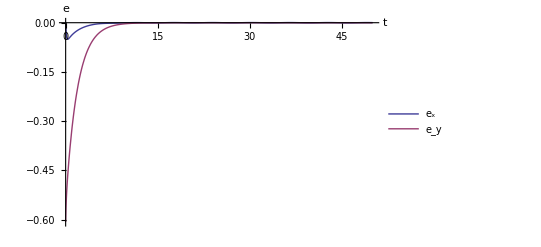

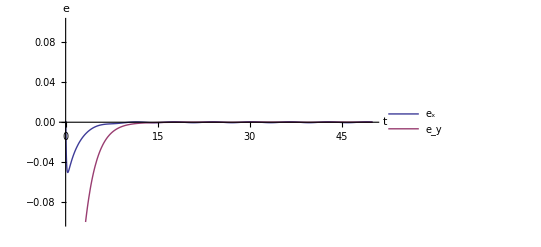

Export::nodir: Directory "C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\" does not exist.

Export::noopen: Cannot open "C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\inz_offu_phi_lin_dyn_0_1.pdf".

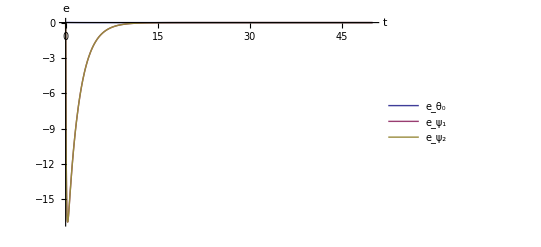

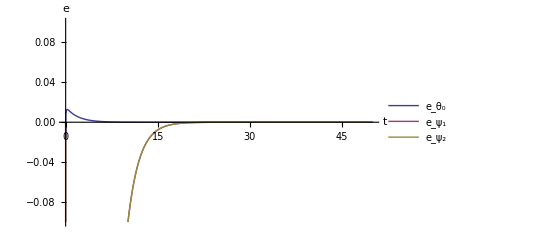

Export::nodir: Directory "C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\" does not exist.

Export::noopen: Cannot open "C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\inz_offu_phi_lin_dyn_0_2.pdf".

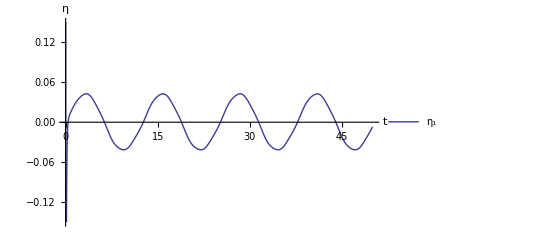

Export::nodir: Directory "C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\" does not exist.

General::stop: Further output of Export :: nodir will be suppressed during this calculation.

Export::noopen: Cannot open "C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\inz_offu_phi_lin_dyn_0_3.pdf".

General::stop: Further output of Export :: noopen will be suppressed during this calculation.

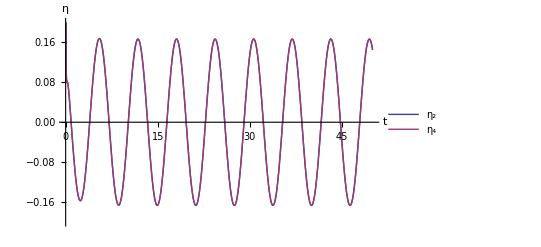

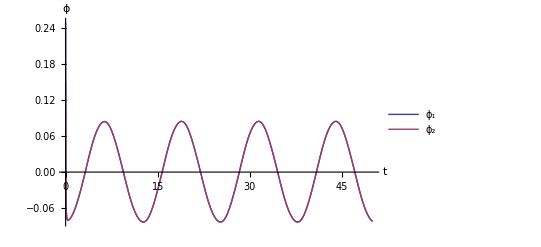

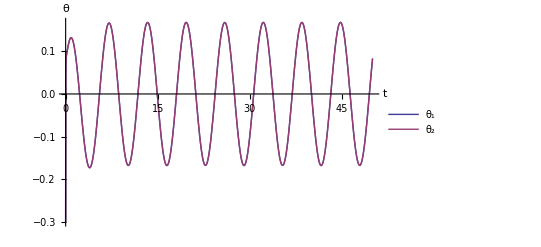

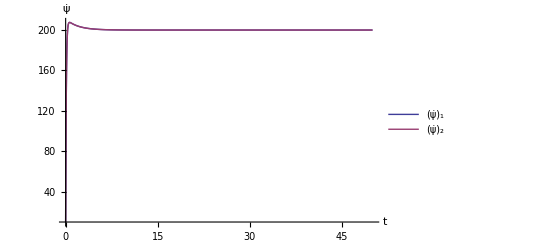

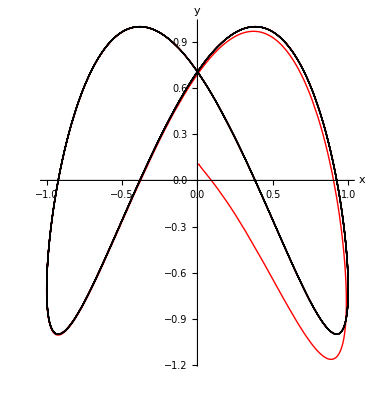

```mathematica
h={x[t],y[t],Subscript[θ, 0][t],Subscript[ψ, 1][t],Subscript[ψ, 2][t]};
zakres={-0.1,0.1};
wirowanie = 200;
tmax=50;
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0.0, Subscript[ϕ, 1][0]==0.25, Subscript[θ, 1][0]== -0.3, Subscript[ψ, 1][0]==0,Subscript[ϕ, 2][0]== 0.15, Subscript[θ, 2][0]==-0.3, Subscript[ψ, 2][0]==0(*,WhenEvent[Subscript[θ, 0][t]>2Pi,Subscript[θ, 0][t]->0]*)};
{xd[t_],yd[t_]}=osemka[t,1];
θd[t_] =0;(*If[ArcTan[xd'[t],yd'[t]]>-Pi/2,ArcTan[xd'[t],yd'[t]],ArcTan[xd'[t],yd'[t]]+2Pi];*)(*Pi/2+t/3;*)
hd = {xd[t],yd[t], θd[t], wirowanie*t, wirowanie*t};
{test,sterowanie} = wyliczSterowanie[hd,h,10,5];
test//MatrixForm
rozwiazanie = rozwiazRownania[sterowanie,test, q0, tmax];
wyrysuj[rozwiazanie,tmax,True,0];
```

```mathematica
h={x[t],y[t],Subscript[θ, 0][t],Subscript[ψ, 1][t],Subscript[ψ, 2][t]};
wirowanie = 200;
tmax=50;
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0.4, Subscript[ϕ, 1][0]==0.15, Subscript[θ, 1][0]== -0.3, Subscript[ψ, 1][0]==0,Subscript[ϕ, 2][0]== 0.25, Subscript[θ, 2][0]==-0.3, Subscript[ψ, 2][0]==0};

For[i=0,i<4,i++,
Print[i];
Which[i==0,{xd[t_],yd[t_]}=osemka[t,1],i==1,{xd[t_],yd[t_]}=kolo[t,3,1],i==2,{xd[t_],yd[t_]}=liniaX[t,3,1],True,{xd[t_],yd[t_]}=kwadrat[t,3,5]];
θd[t_] = 0;(*ArcTan[xd[t],yd[t]]*);
hd = {xd[t],yd[t], θd[t], wirowanie*t, wirowanie*t};
sterowanie = wyliczSterowanie[h,hd,4,2];
{test,sterowanie} = wyliczSterowanie[hd,h,4,2];
rozwiazanie = rozwiazRownania[sterowanie,test, q0, tmax];
wyrysuj[rozwiazanie, tmax,False];
];
```

0

0

Inverse::sing: Matrix {{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}} is singular.

-(R^3 Cos[θ_1[t]]^2 Cos[ϕ_1[t]] Sin[θ_2[t]] Sin[ϕ_2[t]] η_3[t]^2 η_5[t])/(2 l)

1

0

Inverse::sing: Matrix {{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}} is singular.

-(R^3 Cos[θ_1[t]]^2 Cos[ϕ_1[t]] Sin[θ_2[t]] Sin[ϕ_2[t]] η_3[t]^2 η_5[t])/(2 l)

NDSolve::ndsz: At t == 6.45125, step size is effectively zero; singularity or stiff system suspected.

2

0

Inverse::sing: Matrix {{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}} is singular.

General::stop: Further output of Inverse :: sing will be suppressed during this calculation.

-(R^3 Cos[θ_1[t]]^2 Cos[ϕ_1[t]] Sin[θ_2[t]] Sin[ϕ_2[t]] η_3[t]^2 η_5[t])/(2 l)

3

0

-(R^3 Cos[θ_1[t]]^2 Cos[ϕ_1[t]] Sin[θ_2[t]] Sin[ϕ_2[t]] η_3[t]^2 η_5[t])/(2 l)

```mathematica
G2//Simplify//MatrixForm
G3=G2;
G3[[1,1]]=0;
G3[[1,2]]=0;
G3[[2,1]]=0;
G3[[2,2]]=0;
G3[[3,2]]=0;
G3[[3,4]]=0;
G3//Simplify//MatrixForm
```

(R Sin[θ_0[t]] | R Cos[θ_0[t]] Cos[ϕ_1[t]] | R (Sin[θ_0[t]] Sin[θ_1[t]]-Cos[θ_0[t]] Cos[θ_1[t]] Sin[ϕ_1[t]]) | 0 | 0
-R Cos[θ_0[t]] | R Cos[ϕ_1[t]] Sin[θ_0[t]] | -R (Cos[θ_0[t]] Sin[θ_1[t]]+Cos[θ_1[t]] Sin[θ_0[t]] Sin[ϕ_1[t]]) | 0 | 0
0 | -(R Cos[ϕ_1[t]])/(2 l) | (R Cos[θ_1[t]] Sin[ϕ_1[t]])/(2 l) | (R Cos[ϕ_2[t]])/(2 l) | -(R Cos[θ_2[t]] Sin[ϕ_2[t]])/(2 l)
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | Sin[θ_1[t]] | 0 | -Sin[θ_2[t]]
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

(0 | 0 | R (Sin[θ_0[t]] Sin[θ_1[t]]-Cos[θ_0[t]] Cos[θ_1[t]] Sin[ϕ_1[t]]) | 0 | 0
0 | 0 | -R (Cos[θ_0[t]] Sin[θ_1[t]]+Cos[θ_1[t]] Sin[θ_0[t]] Sin[ϕ_1[t]]) | 0 | 0
0 | 0 | (R Cos[θ_1[t]] Sin[ϕ_1[t]])/(2 l) | 0 | -(R Cos[θ_2[t]] Sin[ϕ_2[t]])/(2 l)
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | Sin[θ_1[t]] | 0 | -Sin[θ_2[t]]
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
q[t]
```

{x[t],y[t],θ_0[t],ϕ_1[t],θ_1[t],ψ_1[t],ϕ_2[t],θ_2[t],ψ_2[t]}